Linear ODEs (§10):

```mathematica
Quit[]
```

```mathematica
dv=D[z[t],{t,2}]==2.5*D[z[t],t]-z[t]
```

z''[t]==-z[t]+2.5 z'[t]

```mathematica
DSolveValue[dv,z[t],t]
```

ⅇ^(0.5 t) C[1]+ⅇ^(2. t) C[2]

```mathematica
init={z[0]==z0,z'[0]==v0}
```

{z[0]==z0,z'[0]==v0}

```mathematica
DSolveValue[{dv,init},z[t],t]
```

0.666667 (-1. ⅇ^(0.5 t) v0+1. ⅇ^(2. t) v0+2. ⅇ^(0.5 t) z0-0.5 ⅇ^(2. t) z0)

```mathematica
z0=3
v0=3
DSolveValue[{dv,init},z[t],t]
```

3

3

2. (1. ⅇ^(0.5 t)+0.5 ⅇ^(2. t))

```mathematica
Quit[]
```

```mathematica
eqX=D[x[t],t]==2*x[t]+y[t]
eqY=D[y[t],t]==x[t]+2*y[t]
```

x'[t]==2 x[t]+y[t]

y'[t]==x[t]+2 y[t]

```mathematica
sysODE={eqX,eqY}
DSolveValue[sysODE,{x[t],y[t]},t]
```

{x'[t]==2 x[t]+y[t],y'[t]==x[t]+2 y[t]}

{1/2 ⅇ^t (1+ⅇ^(2 t)) C[1]+1/2 ⅇ^t (-1+ⅇ^(2 t)) C[2],1/2 ⅇ^t (-1+ⅇ^(2 t)) C[1]+1/2 ⅇ^t (1+ⅇ^(2 t)) C[2]}

```mathematica
init={x[0]==x0,y[0]==y0}
DSolveValue[{sysODE,init},{x[t],y[t]},t]
```

{x[0]==x0,y[0]==y0}

{1/2 ⅇ^t (x0+ⅇ^(2 t) x0-y0+ⅇ^(2 t) y0),1/2 ⅇ^t (-x0+ⅇ^(2 t) x0+y0+ⅇ^(2 t) y0)}

```mathematica
x0==2
y0==4
DSolveValue[{sysODE,init},{x[t],y[t]},t]
```

x0==2

y0==4

{1/2 ⅇ^t (x0+ⅇ^(2 t) x0-y0+ⅇ^(2 t) y0),1/2 ⅇ^t (-x0+ⅇ^(2 t) x0+y0+ⅇ^(2 t) y0)}

```mathematica
Quit[]
```

{x'[t]==-x[t]-y[t],y'[t]==x[t]-y[t]}

{2 ⅇ^-t (Cos[t]-2 Sin[t]),2 ⅇ^-t (2 Cos[t]+Sin[t])}

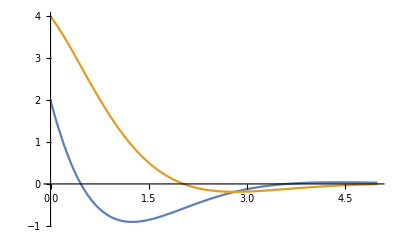

```mathematica
eqX=D[x[t],t]==-x[t]-y[t];
eqY=D[y[t],t]==x[t]-y[t];
sysODE={eqX,eqY}
init={x[0]==2,y[0]==4};
sol=DSolveValue[{sysODE,init},{x[t],y[t]},t]
Plot[sol,{t,0,5},PlotRange->Full]
```

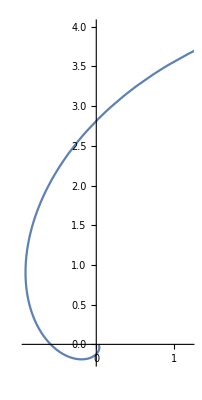

```mathematica
ParametricPlot[sol,{t,0,5}]
```